```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,VectorPlot, VectorPlot3D,StreamPlot,RevolutionPlot3D,ContourPlot3D, Graphics3D}, BaseStyle->{16,FontFamily->"Times"},ImageSize->Small];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

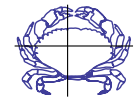
```mathematica
{P1=-Graphics-,P2=-Graphics-,P3=-Graphics-,P4=-Graphics-}
```

```mathematica
P={P1,P2,P3,P4};
```

```mathematica
M1=PopupMenu[Dynamic[n],{1->"Pterodactyl",2->"Snowflake" ,3->"Triceratops ",4->"Crab"}]
```

```mathematica
{M1,Dynamic[Show[P[[n]]]]}
```